# Oscilador Armónico Relativista (oscilador de Dirac)

## Declaración de variables e índices

ca: Constante del oscilador

m: Masa del oscilador

r: Radio del oscilador
p: Momento del oscilador

w: Frecuencia del oscilador

n, j, l1, l2, eme: Números cuánticos (principal (N=2*n+l/N es el principal), momento angular total, momento angular orbital, momento magnético (j_{z}))

p: Paridad

θ,ϕ: Ángulos

# cuánticos: 
N=0(?),1,2,3...=2*n+l
j=1/2,3/2,5/2...,N-1-1/2/N-1+1/2 (depende de la paridad?)(momento angular total)
l=0,...,N-1:0,...,2*n+l-1 (momento angular orbital)
j=l+-1/2(j>=1/2) 
m=-j,...,j (+-1/2)(número cuántico momento magnético)
s=1/2 (momento angular spín)
m_s=+-1/2 (proyección spín)
l1=j+p/2
l2=j-p/2
Definiré el # cuántico principal, a partir de ahí me da un rango de valores para l, defino j (que es común para ambos espinores) y dependiendo de la paridad, defino l’=2*j-l (así ni siquiera necesito definir la paridad)

## Caso no relativista, ecuación de Schrödinger

```mathematica
psi[n_,m_,w_,r_]:=1/Sqrt[2^n*Factorial[n]]*(m*w/Pi*ℏ)^(1/4)*E^(-m*w*r^(2)/(2*ℏ))*HermiteH[n,Sqrt[m*w/ℏ]*r]
psiNatural[n_,m_,w_,r_]:=1/Sqrt[2^n*Factorial[n]]*(m*w/Pi)^(1/4)*E^(-m*w*r^(2)/(2))*HermiteH[n,Sqrt[m*w]*r]

xi[n_,m_,w_,r_]:=Conjugate[psiNatural[n,m,w,r]].psiNatural[n,m,w,r]
densidad[n_,m_,w_,r_]:=Abs[psiNatural[n,m,w,r]]^2
normaliza[n_,m_,w_]:=NIntegrate[xi[n,m,w,r],{r,0,10}]


densidadnormal[n_,m_,w_,r_]:=densidad[n,m,w,r]/normaliza[n,m,w]
densidadnormal[1,1,1,1]
```

NIntegrate::inumr: The integrand (√2 ⅇ^(-1/2 Conjugate[r]^2) Conjugate[r])/π^(1/4).(√2 ⅇ^(-r^2/2) r)/π^(1/4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

2/(ⅇ √π NIntegrate[xi[1,1,1,r],{r,0,10}])

```mathematica
Plot[xi[3,1,1,r],{r,-10,10},PlotRange->All]
```

-Graphics-

```mathematica
Flatten[xi[3,1,1,5]]
```

55225/(3 ⅇ^25 √π)

```mathematica
densidadnormal[n_,m_,w_,r_]:=Conjugate[psiNatural[n,m,w,r]].psiNatural[n,m,w,r]/NIntegrate[xi[n,m,w,r],{r,-10,10}]
densidadnormal[1,1,1,1]
```

NIntegrate::itraw: Raw object 1 cannot be used as an iterator.

((√(2/ⅇ))/π^(1/4).(√(2/ⅇ))/π^(1/4))/NIntegrate[xi[1,1,1,1],{1,-10,10}]

```mathematica
Manipulate[Plot[densidadnormal[n,w,r],{r,0,10}],{n,1,5,1},{w,1,5},PlotRange->All, PlotLabel->"Entropía Shannon (parte radial)",Frame->True,FrameLabel->{"n","S"}]
```

```mathematica
dens1[r_]:=densidad[1,1,1,r]/NIntegrate[densidad[1,1,1,r],{r,-5,5}]
dens1[3]
```

```mathematica
Plot[dens1[r],{r,0,5}]
NIntegrate[xi[n,m,w,r],{r,-10,10}]
```

## Parte Radial

Constante de normalización (radial), componente “pequeña”, componente “grande”

```mathematica
ca[m_,w_,n_,l_,p_]:= ((m*w)/π)^(1/4)((n!2^(n+l-p/2+3/2))/(2*n+2*l+1-2*p)!!)^(1/2)*((n+l+1+p/2)^3+(n+l-p/2)^2)^(-1/2)
Gpequeña[r_,m_,w_,n_,l_]:=ca[m,w,n,l,-1]*(√(m*w)*r)^(l+1)*Exp[-m*w*r^2/2]*Hypergeometric1F1[-n,l+3/2,m*w*r^2]
Fgrande[r_,m_,w_,n_,l_]:=ca[m,w,n,l,1]*(√(m*w)*r)^(l+1)*Exp[-m*w*r^2/2]*Hypergeometric1F1[-n,l+3/2,m*w*r^2]
```

Densidad Radial en espacio momentos

DensidadRadialP[mom_,m_,w_,n_,l1_]= (Abs[FourierTransform[Fgrande[r,m,w,n,l1],r, mom]])^2+(Abs[FourierTransform[Gpequeña[r,m,w,n,l1-1],r, mom]])^2
 tarda mucho en evaluar

```mathematica
DensidadRadialP[mom_,w_,n_,l1_]:= (Abs[FgrandeP[mom,1.0,w,n,l1]])^2+(Abs[GpequeñaP[mom,1.0,w,n,l1-1]])^2
DensidadRadialP[mom,1,5,1]
DensidadRadialP[-8,1,5,1]
(Abs[FgrandeP[3,1.0,1,5,1]])^2
(Abs[FourierTransform[Fgrande[r,1.0,1,5,1],r,mom]])^2
(Abs[FourierTransform[Fgrande[r,1,1,5,1],r,mom]])^2
```

2 π Abs[Gpequeña DiracDelta[mom]]^2+Abs[(Fgrande √(2 π) DiracDelta[mom])[mom,1.,1,5,1]]^2

Abs[FourierTransform[Gpequeña,r,-8]]^2+Abs[(Fgrande √(2 π) DiracDelta[mom])[-8,1.,1,5,1]]^2

Abs[(Fgrande √(2 π) DiracDelta[mom])[3,1.,1,5,1]]^2

9.30551×10^-10 ⅇ^(-1. Re[mom^2]) Abs[127.031-2047.97 mom^2+3359.06 mom^4-1786.25 mom^6+380. mom^8-33.5 mom^10+1. mom^12]^2

(8192 ⅇ^(-Re[mom^2]) Abs[4065-65535 mom^2+107490 mom^4-57160 mom^6+12160 mom^8-1072 mom^10+32 mom^12]^2)/(5085983253876525 √π)

```mathematica
DensidadRadialPc[mom_,w_,n_,l1_]:=FourierTransform[DensidadRadial[r,w,n,l1, l1-1],r,mom]
DensidadRadialPc[mom,w,n,l1]

FourierTransform[DensidadRadial[r,w,n,l1, l1-1],{r},{mom}]
Plot3D[%,{mom,0.1,1},PlotRange->All,Mesh->False]
```

```mathematica
FourierTransform[DensidadRadial[r,1,2,1, 0],r,mom]
Plot[%,{FourierTransform[DensidadRadial[r,1,2,1, 0],r,mom],0.1,1},PlotRange->All]
```

$Aborted

-Graphics-

```mathematica
DensidadRadialP[0,1,5,2]
```

2 π Abs[Fgrande DiracDelta[0]]^2+2 π Abs[Gpequeña DiracDelta[0]]^2

```mathematica
Plot[DensidadRadialP[mom,1,5,2],{mom,-1,1}]
Manipulate[Plot[DensidadRadialP[mom,w,n,l1],{mom,-2,2}],{w,1,5},{n,1,2,1},{l1,0,n-1,1}]
Manipulate[Plot[(Abs[FgrandeP[mom,1.0,w,n,l1]])^2+(Abs[GpequeñaP[mom,1.0,w,n,l1-1]])^2,{mom,-2,2}],{w,1,5},{n,1,2,1},{l1,0,n-1,1}]
```

```mathematica
Manipulate[Plot[(Abs[FourierTransform[Fgrande[r,1.0,w,n,l1],r,mom]])^2+(Abs[FourierTransform[Gpequeña[r,1.0,w,n,l1-1],r,mom]])^2,{mom,-0.5,0.5}],{w,1,2},{n,1,2,1},{l1,0,n-1,1}]
```

```mathematica
Plot[{(Abs[FourierTransform[Fgrande[r,1,1,5,2], r, mom]])^2,(Abs[FourierTransform[Gpequeña[r,1,1,5,1], r, mom]])^2},{mom,-0.5,0.5}]
Manipulate[Plot[{(Abs[FourierTransform[Fgrande[r,1,w,n,l1], r, mom]])^2,(Abs[FourierTransform[Gpequeña[r,1,w,n,l1-1], r, mom]])^2},{mom,-0.5,0.5}],{w,1,2},{n,1,3,1},{l1,0,n-1}]
```

Aquí al representar, puede haber problemas con el intervalo de j.  Se me imprime sin errores, pero no me representa nada. Me gustaría conocer la forma que tiene la densidad radial en el espacio de momentos. Cómo la interpreto? 

La DensidadRadialP me da cero para cualquier valor, por eso no me imprime nada 
Tiene que ser un fallo de mom. En principio, no debe ser muy alto porque si no la exponencial enseguida se va a 0. 
También, en su dominio se incluyen los negativos... Pero mom puede ser negativo? Es la componente x del momento lineal cuando sólo hay movimiento en ese eje. 
Para la antipartícula? 

Dónde está función en el espacio de momentos que se me ploteaba bien? Era la densidad en el espacio de momentos.

```mathematica
TablaDensidadRadialP=Table[{w,n,l1,DensidadRadialP[mom,w,n,l1]},{w,1,10},{n,1,5,1},{l1,0,n-1}];
```

De la segunda forma, ya conseguí la tabla. De la primera forma, no me da error pero tampoco me imprime nada

```mathematica
TablaDensidadRadialEp=Table[{n,l1,(Abs[FourierTransform[Fgrande[r,1,w,n,l1], r, mom]])^2+(Abs[FourierTransform[Gpequeña[r,1,w,n,l1-1], r, mom]])^2},{w,1,2},{n,1,2,1},{l1,0,n-1}]
```

Me da error y no sé cómo resolverlo. El problema viene con el intervalo de representación de mom. 

Si tengo dos funciones FgrandeP con distintos argumentos de entrada y le doy los que coinciden con una de las funciones, es esa la que coge? 
CAMBIAR NOMBRE FUNCIÓN 

 Necesito alguna gráfica. Por lo menos tengo las tablas

## Densidad

Densidad Radial

```mathematica
DensidadRadial[r_,w_,n_,l1_, l2_]:= (Abs[Fgrande[r,1.0,w,n,l1]])^2+(Abs[Gpequeña[r,1.0,w,n,l2]])^2


Manipulate[Plot[DensidadRadial[r,w,n,l1,l1-1],{r,-10,10}],{w,1,5},{n,1,5,1},{l1,0,n-1,1}]
Flatten[DensidadRadial[r,1,1,1,2]]
```

0.0333408 ⅇ^(-1. Re[r^2]) Abs[r^2 (1.-0.4 r^2)]^2+0.000346573 ⅇ^(-1. Re[r^2]) Abs[r^3 (1.-0.285714285714286 r^2)]^2

Densidad Angular

```mathematica
p:=1
DensidadAngular1[l1_,l2_,j_,eme_, θ_,ϕ_]:=(ConjugateTranspose[If[p==1,{{Sqrt[(j+eme)/(2*j)]*SphericalHarmonicY[l2,eme-1/2, θ,ϕ]},{Sqrt[(j-eme)/(2*j)]*SphericalHarmonicY[l2,eme+1/2, θ,ϕ]}},{{-Sqrt[(j-eme+1)/(2*j+2)]*SphericalHarmonicY[l2,eme-1/2, θ,ϕ]},{Sqrt[(j+eme+1)/(2*j+2)]*SphericalHarmonicY[l2,eme+1/2, θ,ϕ]}}]]).(If[p==1,{{Sqrt[(j+eme)/(2*j)]*SphericalHarmonicY[l2,eme-1/2, θ,ϕ]},{Sqrt[(j-eme)/(2*j)]*SphericalHarmonicY[l2,eme+1/2, θ,ϕ]}},{{-Sqrt[(j-eme+1)/(2*j+2)]*SphericalHarmonicY[l2,eme-1/2, θ,ϕ]},{Sqrt[(j+eme+1)/(2*j+2)]*SphericalHarmonicY[l2,eme+1/2, θ,ϕ]}}])


DensidadAngular2[l1_,l2_,j_,eme_, θ_,ϕ_]:=(ConjugateTranspose[If[p==1,{{Sqrt[(j+eme)/(2*j)]*SphericalHarmonicY[l1,eme-1/2, θ,ϕ]},{Sqrt[(j-eme)/(2*j)]*SphericalHarmonicY[l1,eme+1/2, θ,ϕ]},{-Sqrt[(j-eme+1)/(2*j+2)]*SphericalHarmonicY[l1,eme-1/2, θ,ϕ]},{Sqrt[(j+eme+1)/(2*j+2)]*SphericalHarmonicY[l1,eme+1/2, θ,ϕ]}}]]).(If[p==1,{{Sqrt[(j+eme)/(2*j)]*SphericalHarmonicY[l1,eme-1/2, θ,ϕ]},{Sqrt[(j-eme)/(2*j)]*SphericalHarmonicY[l1,eme+1/2, θ,ϕ]},{-Sqrt[(j-eme+1)/(2*j+2)]*SphericalHarmonicY[l1,eme-1/2, θ,ϕ]},{Sqrt[(j+eme+1)/(2*j+2)]*SphericalHarmonicY[l1,eme+1/2, θ,ϕ]}}])
```

```mathematica
DensidadAngularTotal[l1_,j_,eme_, θ_,ϕ_]:=DensidadAngular1[l1,l1-1,j,eme, θ,ϕ]+DensidadAngular2[l1,l1-1,j,eme, θ,ϕ]
```

Normalizando la densidad

```mathematica
DensidadNormal[r_,w_,n_,l1_,l2_] :=  DensidadRadial[r,w,n,l1, l2]/NIntegrate[DensidadRadial[r,w,n,l1,l2],{r,0,10}]
norma[w_,n_,l1_,l2_]:=NIntegrate[DensidadRadial[r,w,n,l1,l2],{r,0,10}]
DensidadNormalc[r_,w_,n_,l1_,l2_]:=DensidadRadial[r,w,n,l1, l2]/norma[w,n,l1,l2]
```

```mathematica
DensidadAngularNormal[l1_,j_,eme_, θ_,ϕ_]:=DensidadAngularTotal[l1,j,eme, θ,ϕ]/NIntegrate[DensidadAngularTotal[l1,j,eme, θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi}]
normang[l1_,j_,eme_]:=NIntegrate[DensidadAngularTotal[l1,j,eme, θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi}]
DensidadAngularNormalc[l1_,j_,eme_, θ_,ϕ_]:=DensidadAngularTotal[l1,j,eme, θ,ϕ]/normang[l1,j,eme]
```

Densidad Total

```mathematica
DensidadTotal[l1_,l2_,j_,eme_,w_,n_,r_,θ_,ϕ_]:=DensidadAngularTotal[l1,j,eme, θ,ϕ]*DensidadRadial[r,w,n,l1, l2]
```

```mathematica
DensidadTotalc[l1_,l2_,j_,eme_,w_,n_,r_,θ_,ϕ_]:=DensidadAngularNormalc[l1,j,eme, θ,ϕ]*DensidadNormalc[r,w,n,l1, l2];
```

```mathematica
DensidadTotalNorm[l1_,l2_,j_,eme_,w_,n_,r_,θ_,ϕ_]:=DensidadTotal[l1,l2,j,eme,w,n,r,θ,ϕ]/NIntegrate[DensidadTotal[l1,l2,j,eme,w,n,r,θ,ϕ],{r,1,10}{θ,0,Pi},{ϕ,0,2*Pi}]

Consta[l1_,l2_,j_,eme_,w_,n_]:=NIntegrate[DensidadTotal[l1,l2,j,eme,w,n,r,θ,ϕ],{r,0,10}{θ,0,Pi},{ϕ,0,2*Pi}]
DensidadTotalNormc[l1_,l2_,j_,eme_,w_,n_,r_,θ_,ϕ_]:=DensidadTotal[l1,l2,j,eme,w,n,r,θ,ϕ]/Consta[l1,l2,j,eme,w,n]
```

```mathematica
Manipulate[Plot[DensidadNormalc[r,w,n,j+1/2,j-1/2],{r,0,10}],{w,1,2,1},{n,1,3,1},{j,1/2,n-1/2,1}]
Manipulate[Plot[DensidadRadial[r,w,n,j+1/2,j-1/2],{r,0,10}],{w,1,2,1},{n,1,3,1},{j,1/2,n-1/2,1}]
```

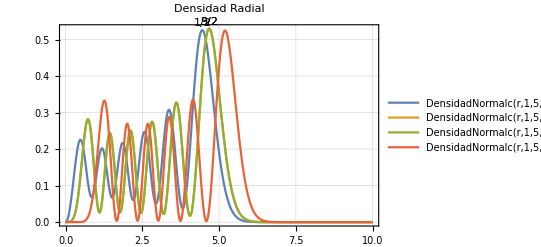

```mathematica
Plot[{DensidadNormalc[r,1,5,1,0],DensidadNormalc[r,1,5,2,1],DensidadNormalc[r,1,5,2,1],DensidadNormalc[r,1,5,5,4]},{r,0,10},PlotTheme->"Detailed",PlotLabel->"Densidad Radial",PlotLabels->Placed[{"1/2","3/2","9/2"},Above],PlotRange->All]
```

```mathematica
Manipulate[Plot[{DensidadNormalc[r,w,n,j+1/2,j-1/2],DensidadRadial[r,w,n,j+1/2,j-1/2]},{r,0,10}],{w,1,2,1},{n,1,3,1},{j,1/2,n-1/2,1}]
```

```mathematica
Manipulate[Plot3D[DensidadAngularNormalc[j+1/2,j,eme, θ,ϕ],{θ,0,Pi},{ϕ,0,2*Pi}],{n,1,5,1},{j,1/2,n-1/2,1},{eme,{1/2,3/2,5/2,9/2}}]
```

```mathematica
Manipulate[Plot3D[DensidadAngularTotal[j+1/2,j,eme, θ,ϕ],{θ,0,Pi},{ϕ,0,2*Pi},Background->White,AxesStyle->Black, PlotStyle->Directive[Orange, Specularity[White,50]],Mesh->{{Pi/4,Pi/2,3/4*Pi},{Pi/2,Pi,3/2*Pi}},PlotTheme->"Detailed",PlotLabel->"Densidad angular"],{n,1,8,1},{j,1/2,n-1/2,1},{eme,{1/2,3/2,5/2,7/2,9/2}}]
```

```mathematica
Manipulate[NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r, θ,ϕ],{θ,0,Pi},{ϕ,0,2*Pi},{r,0,2}],{n,1,8,1},{j,1/2,n-1/2,1},{w,1,2,1},{eme,{1/2,3/2,5/2,9/2}}]
```

```mathematica
Manipulate[Plot3D[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r, θ,ϕ],{θ,0,Pi},{ϕ,0,2*Pi},Background->White,AxesStyle->Black, PlotStyle->Directive[Orange, Specularity[White,50]],Mesh->{{Pi/4,Pi/2,3/4*Pi},{Pi/2,Pi,3/2*Pi}},PlotTheme->"Detailed",PlotLabel->"Densidad total"],{r,1,2},{n,1,2,1},{j,1/2,n-1/2,1},{w,1,2,1},{eme,{1/2,3/2,5/2,9/2}}]
```

```mathematica
Manipulate[Plot3D[{DensidadTotal[1,0,1/2,1/2,1,1,r, θ,ϕ]/0.06899816493185534,DensidadTotal[1,0,1/2,1/2,1,2,r, θ,ϕ]/0.00839056227753391,DensidadTotal[1,0,1/2,1/2,1,3,r, θ,ϕ]/0.0017451439051829863},{θ,0,Pi},{ϕ,0,2*Pi},PlotLegends->{n=1,n=2,n=3},Mesh->{{Pi/4,Pi/2,3/4*Pi},{Pi/2,Pi,3/2*Pi}},PlotTheme->"Detailed",PlotLabel->"Densidad total"],{r,1,10}]
```

```mathematica
Manipulate[Plot3D[{DensidadTotal[1,0,1/2,1/2,1,5,r, θ,ϕ]/0.00023708856008660328,DensidadTotal[2,1,3/2,1/2,1,5,r, θ,ϕ]/0.000015916141900001865,DensidadTotal[3,2,5/2,1/2,1,5,r, θ,ϕ]/2.167670432574334*10^-6},{θ,0,Pi},{ϕ,0,2*Pi},PlotLegends->{j=1/2,j=3/2,j=5/2},Mesh->{{Pi/4,Pi/2,3/4*Pi},{Pi/2,Pi,3/2*Pi}},PlotTheme->"Detailed",PlotLabel->"Densidad total"],{r,1,10}]
```

```mathematica
Manipulate[Plot3D[{DensidadTotal[5,4,9/2,1/2,1,5,r, θ,ϕ]/8.806970312772152*10^-8,DensidadTotal[5,4,9/2,3/2,1,5,r, θ,ϕ]/5.957894556188148*10^-8,DensidadTotal[5,4,9/2,9/2,1,5,r, θ,ϕ]/3.7448448496400995*10^-8},{θ,0,Pi},{ϕ,0,2*Pi},PlotLegends->{eme=1/2,eme=3/2,eme=9/2},Mesh->{{Pi/4,Pi/2,3/4*Pi},{Pi/2,Pi,3/2*Pi}},PlotTheme->"Detailed",PlotLabel->"Densidad total"],{r,1,10}]
```

En cuanto pongo el normalizado con c (cada densidad, radial y angular, normalizada; es decir cada densidad dividida por el valor que tiene cuando integramos en su variable) para la densidad angular o la total, me da un plano. 
Puedo imprimirlo como densidadangular/total original, dividiéndolo entre el número apropiado
El problema con usar la densidad angular y total no normalizada es que los valores no son los correctos, aunque me de la forma correcta

MEDIDAS TEÓRICO INFORMACIONALES

### Entropía de Shannon

```mathematica
loga [r_,w_,n_,j_]:=DensidadRadial[r,w,n,j+1/2,j-1/2]*Log[DensidadRadial[r,w,n,j+1/2,j-1/2]]
Shannon[w_,n_,j_]=  -1.0*NIntegrate[loga[r,w,n,j], {r, 0, 10}];
Shanon:=-1.0*NIntegrate[loga[r,1,1,3/2],{r,0,10}]
Shanon:=-1.0*NIntegrate[loga[r,w,n,j],{r,0,10}]
Shannon[1,1,3/2]
Shanon
```

```mathematica
Manipulate[(-1.0/NIntegrate[DensidadRadial[r,w,n,j+1/2,j-1/2],{r,0,10}])*NIntegrate[DensidadRadial[r,w,n,j+1/2,j-1/2]*Log[DensidadRadial[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
Manipulate[-1.0*NIntegrate[DensidadRadial[r,w,n,j+1/2,j-1/2]*Log[DensidadRadial[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
```

```mathematica
Manipulate[(-1.0/NIntegrate[DensidadNormal[r,w,n,j+1/2,j-1/2],{r,0,10}])*NIntegrate[DensidadNormal[r,w,n,j+1/2,j-1/2]*Log[DensidadNormal[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
Manipulate[-1.0*NIntegrate[DensidadNormal[r,w,n,j+1/2,j-1/2]*Log[DensidadNormal[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
```

```mathematica
Manipulate[(-1.0/NIntegrate[DensidadNormalc[r,w,n,j+1/2,j-1/2],{r,0,10}])*NIntegrate[DensidadNormalc[r,w,n,j+1/2,j-1/2]*Log[DensidadNormalc[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
Manipulate[-1.0*NIntegrate[DensidadNormalc[r,w,n,j+1/2,j-1/2]*Log[DensidadNormalc[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
```

```mathematica
Manipulate[Plot[-1.0*NIntegrate[DensidadNormal[r,w,n,j+1/2,j-1/2]*Log[DensidadNormal[r,w,n,j+1/2,j-1/2]], {r, 0, 10}],{n,1,3}],{w,1,5},{j,1/2,n-1/2}]
```

```mathematica
Manipulate[(-1.0/NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,{-1/2,1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2}}]
Manipulate[-1.0*NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,{-1/2,1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2}}]
```

```mathematica
Manipulate[(-1.0/NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,{-1/2,1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2}}]
Manipulate[-1.0*NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,{-1/2,1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2}}]
```

```mathematica
Table[{j,-1.0*NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,1/2,1,1,r,θ,ϕ]*Log[DensidadTotal[j+1/2,j-1/2,j,1/2,1,1,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]},{j,1/2,3/2,1}]
Table[{n,-1.0*NIntegrate[DensidadTotalc[3,2,5/2,3/2,1,n,r,θ,ϕ]*Log[DensidadTotal[3,2,5/2,3/2,1,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]},{n,1,8}]
```

{{1/2,{{5.96387}}},{3/2,{{7.57996}}}}

{{1,{{8.90291}}},{2,{{11.4038}}},{3,{{13.3335}}},{4,{{14.9148}}},{5,{{16.2583}}},{6,{{17.4282}}},{7,{{18.4651}}},{8,{{19.3969}}}}

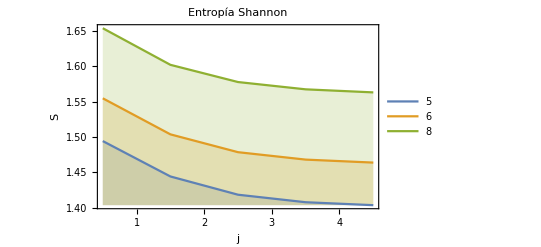

```mathematica
DiscretePlot[{-1.0*NIntegrate[DensidadNormal[r,1,5,j+0.5,j-0.5]*Log[DensidadNormal[r,1,5,j+0.5,j-0.5]],{r,0,10}],-1.0*NIntegrate[DensidadNormal[r,1,6,j+0.5,j-0.5]*Log[DensidadNormal[r,1,6,j+0.5,j-0.5]],{r,0,10}],-1.0*NIntegrate[DensidadNormal[r,1,8,j+0.5,j-0.5]*Log[DensidadNormal[r,1,8,j+0.5,j-0.5]],{r,0,10}]},{j,0.5,4.5,1},PlotRange->All, Joined->True,PlotLabel->Entropía Shannon,PlotLegends->{n=5,n=6,n=8},Frame->True,FrameLabel->{"j","S"}]
```

No tiene sentido plotear para n=2, j=9/2 porque no existe. existe hasta el 3/2 con esta paridad.

```mathematica
TablaShannonNormal = Table[{j,-1.0*NIntegrate[DensidadNormal[r,1,5,j+0.5,j-0.5]*Log[DensidadNormal[r,1,5,j+0.5,j-0.5]],{r,0,10}]},{j,0.5,4.5,1}]
```

{{0.5,1.49428},{1.5,1.44415},{2.5,1.4183},{3.5,1.40766},{4.5,1.4035}}

```mathematica
TablaShannonNormal //Flatten[#,0]&//Grid
```

0.5 | 1.49428
1.5 | 1.44415
2.5 | 1.4183
3.5 | 1.40766
4.5 | 1.4035

```mathematica
TablaShannonNormal2= Table[{n,-1.0*NIntegrate[DensidadNormal[r,1,n,1,0]*Log[DensidadNormal[r,1,n,1,0]],{r,0,10}],-1.0*NIntegrate[DensidadNormal[r,1,n,2,1]*Log[DensidadNormal[r,1,n,2,1]],{r,0,10}],-1.0*NIntegrate[DensidadNormal[r,1,n,3,2]*Log[DensidadNormal[r,1,n,3,2]],{r,0,10}]},{n,1,3,1}]
```

{{1,1.03035,1.02314,0.996221},{2,1.21421,1.17973,1.15171},{3,1.33343,1.2892,1.26179}}

```mathematica
TablaShannonNormal2 //Flatten[#,0]&//Grid
```

1 | 1.03035 | 1.02314 | 0.996221
2 | 1.21421 | 1.17973 | 1.15171
3 | 1.33343 | 1.2892 | 1.26179

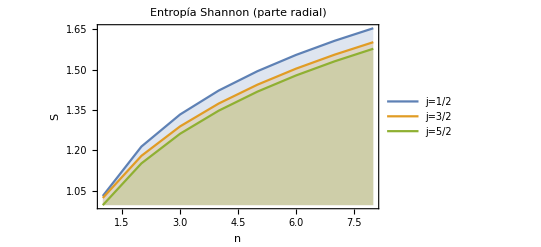

```mathematica
DiscretePlot[{-1.0*NIntegrate[DensidadNormal[r,1,n,1,0]*Log[DensidadNormal[r,1,n,1,0]],{r,0,10}],-1.0*NIntegrate[DensidadNormal[r,1,n,2,1]*Log[DensidadNormal[r,1,n,2,1]],{r,0,10}],-1.0*NIntegrate[DensidadNormal[r,1,n,3,2]*Log[DensidadNormal[r,1,n,3,2]],{r,0,10}]},{n,1,8,1},PlotRange->All, Joined->True,PlotLabel->"Entropía Shannon (parte radial)",Frame->True,FrameLabel->{"n","S"},PlotLegends->{"j=1/2","j=3/2","j=5/2"}]
```

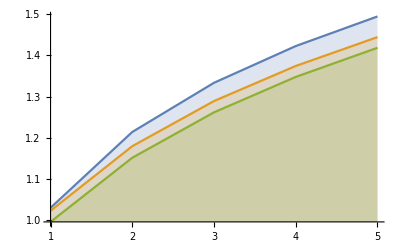

```mathematica
DiscretePlot[{-1.0*NIntegrate[DensidadNormalc[r,1,n,1,0]*Log[DensidadNormalc[r,1,n,1,0]],{r,0,10}],-1.0*NIntegrate[DensidadNormalc[r,1,n,2,1]*Log[DensidadNormalc[r,1,n,2,1]],{r,0,10}],-1.0*NIntegrate[DensidadNormalc[r,1,n,3,2]*Log[DensidadNormalc[r,1,n,3,2]],{r,0,10}]},{n,1,5,1},PlotRange->All, Joined->True]
```

```mathematica
ShannonInt[w_,n_,l1_,l2_]:=-1.0*NIntegrate[DensidadNormal[r,w,n,l1,l2]*Log[DensidadNormal[r,w,n,l1,l2]],{r,0,10}];
Dimensions[ShannonInt[1,1,1,0]]
```

{}

```mathematica
nvalores={2,3,4,5,6,7,8};
wvalores={1,3,5};
arrayr=Table[{w,ShannonInt[w,n,2,1]},{n,nvalores},{w,wvalores}]
```

Image::imgarray: The specified argument {} should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

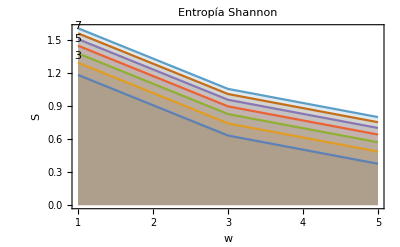

```mathematica
ListPlot[arrayr
,Joined->True
,Frame->True
,FrameLabel->{"w","S"}
,PlotLabels->Placed[{"","3","","5","","7",""},Above]
,Filling->Axis, PlotRange->All
,PlotLabel->"Entropía Shannon",PlotRange->All
,PlotStyle->Table[ColorData["SunsetColors"][i/(Length[valoresn]+1)],{i,1,Length[valoresn]}]
]
```

```mathematica
int[j_,eme_,w_,n_]:=-1.0*NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]
```

```mathematica
valoresj={3/2,5/2};
valoresn={2,3,4,5,6,8};
array=Table[{n,int[j,3/2,1,n][[1,1]]},{j,valoresj},{n,valoresn}];
array//MatrixForm
```

((2
4.14977) | (3
4.269) | (4
4.35804) | (5
4.42984) | (6
4.49042) | (8
4.58968)
(2
4.03726) | (3
4.14672) | (4
4.23173) | (5
4.30167) | (6
4.36132) | (8
4.4598))

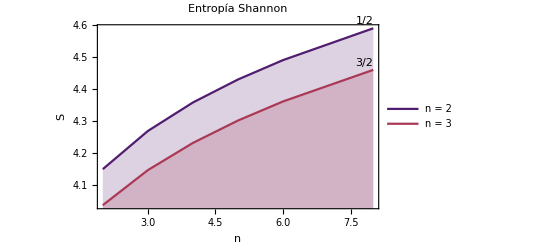

```mathematica
ListPlot[array
,Joined->True
,Frame->True
,FrameLabel->{"n","S"}
,PlotLegends->("n = "<>ToString[#]&)/@valoresn,PlotLabels->Placed[{"1/2","3/2"},Above]
,Filling->Axis, PlotRange->All
,PlotLabel->"Entropía Shannon",PlotRange->All
,PlotStyle->Table[ColorData["SunsetColors"][i/(Length[valoresn]+1)],{i,1,Length[valoresn]}]
]
```

```mathematica
valoresn2={1,8,1};
valoresj2={1/2,3/2,5/2};
array2=Table[{n,int[j,1/2,1,n][[1,1]]},{j,valoresj2},{n,valoresn2}];
```

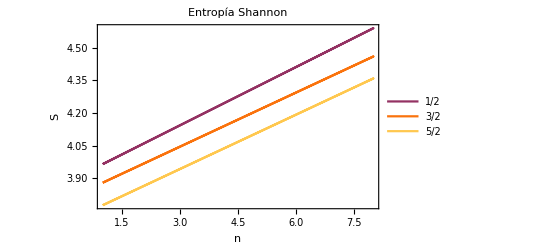

```mathematica
ListPlot[array2
,Joined->True
,Frame->True
,FrameLabel->{"n","S"}
,PlotLegends->{1/2,3/2,5/2}
,Filling->Axis 
,PlotLabel->"Entropía Shannon",PlotRange->All
,PlotStyle->Table[ColorData["SunsetColors"][i/(Length[valoresj2]+1)],{i,1,Length[valoresj2]}]
]
```

```mathematica
TablaShannonValTotal=Table[{eme,int[7/2,eme,1,6][[1,1]]},{eme,{1/2,3/2,5/2,7/2}}]
```

{{1/2,4.18576},{3/2,4.28209},{5/2,4.1609},{7/2,3.93819}}

```mathematica
valoresn2={1,8,1};
valoreseme={1/2,3/2,5/2};
array3=Table[{eme,int[5/2,eme,1,3][[1,1]]},{eme,valoreseme}]
```

{{1/2,4.0429},{3/2,4.08398},{5/2,3.87342}}

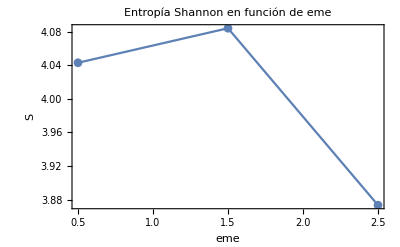

```mathematica
ListPlot[array3
,Frame->True
,Joined->True
,FrameLabel->{"eme","S"}
,PlotMarkers->Automatic,PlotLabel->"Entropía Shannon en función de eme"]
```

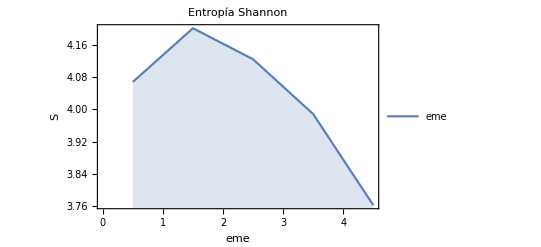

```mathematica
ListPlot[TablaShannonValTotal
,Joined->True
,Frame->True
,FrameLabel->{"eme","S"}
,Filling->Axis 
,PlotLabel->"Entropía Shannon"

]
```

```mathematica
FUNCIONALES COMPARATIVOS:JSD
```

```mathematica
dens[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_,r_,θ_,ϕ_]:=DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]+DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]
```

```mathematica
comp[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=(-1.0/NIntegrate[dens[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[dens[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]*Log[dens[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]
comp1[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=-1.0*NIntegrate[dens[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]*Log[dens[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]
comp[l1,l2,l10,l20,3/2,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]
comp1[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]
```

comp[l1,l2,l10,l20,3/2,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]

comp1[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0,r,θ,ϕ]

```mathematica
jsd[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=1/2*((-1.0/NIntegrate[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]+((-1.0/NIntegrate[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]*Log[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]))
jsd1[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=1/2*(NIntegrate[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]+(NIntegrate[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]*Log[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]))
```

```mathematica
jsdTotal[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=comp[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0]-1/2*((-1.0/NIntegrate[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]+((-1.0/NIntegrate[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]*Log[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]))
```

```mathematica
jsdTotal[2,1,3,2,1/2,3/2,1/2,3/2,6,6,1,1]
```

{{-0.516504}}

```mathematica
jsdTotal1[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=comp[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0]-1/2*jsd[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0]
jsdTotal1[2,1,3,2,1/2,3/2,1/2,3/2,6,6,1,1]
```

{{1.6519}}

```mathematica
jsdTotal2[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=comp1[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0]-1/2*jsd1[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0]
jsdTotal3[l1_,l2_,l10_,l20_,j_,j0_,eme_,eme0_,n_,n0_,w_,w0_]:=comp1[l1,l2,l10,l20,j,j0,eme,eme0,n,n0,w,w0]-1/2*(NIntegrate[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]*Log[DensidadTotalc[l1,l2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]+(NIntegrate[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]*Log[DensidadTotalc[l10,l20,j0,eme0,w0,n0,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}]))
jsdTotal2[2,1,3,2,1/2,3/2,1/2,3/2,6,6,1,1]
jsdTotal3[2,1,3,2,1/2,3/2,1/2,3/2,6,6,1,1]
```

{{9.69324}}

{{11.8301}}

Al normalizar la DensidadTotal directamente en la expresión, se me eleva el valor.

Me dan diferentes jsdTotal y jsdTotal1

```mathematica
jvalores={5/2,7/2,9/2,11/2};
emevalores={1/2,5/2};
array4=Table[{j,jsdTotal[j+1/2,j-1/2,3,2,j,5/2,1/2,eme0,6,6,1,1][[1,1]]},{eme0,emevalores},{j,jvalores}]
```

{{{5/2,-0.693147},{7/2,-0.593952},{9/2,-0.489179},{11/2,-0.489716}},{{5/2,-0.417924},{7/2,-0.34798},{9/2,-0.28405},{11/2,-0.280313}}}

```mathematica
array11=Table[{j,jsdTotal3[j+1/2,j-1/2,3,2,j,5/2,1/2,eme0,6,6,1,1][[1,1]]},{eme0,emevalores},{j,jvalores}]
```

{{{5/2,11.3926},{7/2,11.4802},{9/2,11.6031},{11/2,11.5304}},{{5/2,11.6889},{7/2,11.7179},{9/2,11.7591},{11/2,11.695}}}

```mathematica
array12=Table[{j,jsdTotal2[j+1/2,j-1/2,3,2,j,5/2,1/2,eme0,6,6,1,1][[1,1]]},{eme0,emevalores},{j,jvalores}]
```

{{{5/2,9.26282},{7/2,9.36885},{9/2,9.50617},{11/2,9.44542}},{{5/2,9.60142},{7/2,9.64895},{9/2,9.70459},{11/2,9.65238}}}

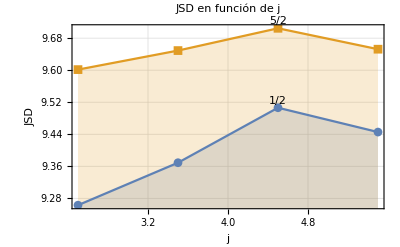

```mathematica
ListPlot[array12
,Frame->True
,Joined->True
,Filling->Axis
,FrameLabel->{"j","JSD"},
PlotRange->All
,PlotTheme->"Detailed"
,PlotMarkers->Automatic,PlotLabel->"JSD en función de j"
,PlotLabels->Placed[{"1/2","5/2"},Above]]
```

```mathematica
nvalores={1,3,5};
array5=Table[{n,jsdTotal[3,2,3,2,5/2,5/2,1/2,eme0,n,6,1,1][[1,1]]},{eme0,{1/2,5/2}},{n,{3,4,5}}]
```

{{{3,-0.459795},{4,-0.508306},{5,Indeterminate}},{{3,-0.287665},{4,-0.313381},{5,Indeterminate}}}

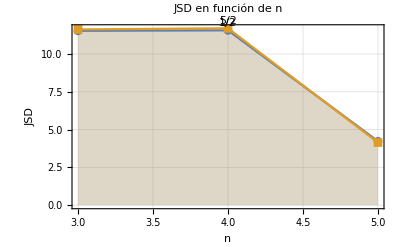

```mathematica
ListPlot[array5,
PlotTheme->"Detailed",
Filling->Axis
,Frame->True
,FrameLabel->{"n","JSD"},
Joined->True,PlotRange->All,PlotLabels->Placed[{"1/2","5/2","7/2"},Above]
,PlotMarkers->Automatic,PlotLabel->"JSD en función de n" 
]
```

```mathematica
jvalores={1/2,3/2,5/2,7/2};
emevalores={1/2,3/2,5/2,7/2};
array4=Table[{eme,jsdTotal2[5,4,4,3,9/2,7/2,eme,eme0,6,6,1,1][[1,1]]},{eme0,emevalores},{eme,emevalores}]
```

{{{1/2,9.19699},{3/2,9.51937},{5/2,9.62144},{7/2,9.59546}},{{1/2,9.55742},{3/2,9.49986},{5/2,9.44032},{7/2,9.4654}},{{1/2,9.60523},{3/2,9.54205},{5/2,9.27706},{7/2,9.088}},{{1/2,9.47817},{3/2,9.4736},{5/2,9.22062},{7/2,8.87107}}}

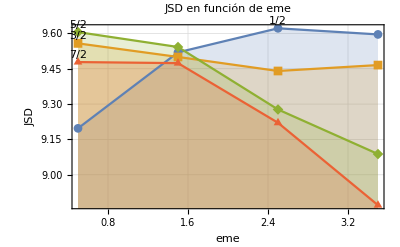

```mathematica
ListPlot[array4
,Frame->True
,Joined->True
,Filling->Axis
,FrameLabel->{"eme","JSD"},
PlotRange->All
,PlotTheme->"Detailed"
,PlotMarkers->Automatic,PlotLabel->"JSD en función de eme"
,PlotLabels->Placed[{"1/2","3/2","5/2","7/2"},Above]]
```

```mathematica
Información de Fisher:
```

```mathematica
Manipulate[(1.0/NIntegrate[DensidadRadial[r,w,n,j+1/2,j-1/2],{r,0,10}])*NIntegrate[ComplexExpand[(Abs[D[DensidadRadial[r,w,n,j+1/2,j-1/2],r]])^2/DensidadRadial[r,w,n,j+1/2,j-1/2]], {r, 1, 10}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
```

```mathematica
Manipulate[(1.0/NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[ComplexExpand[(Abs[D[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,1,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,1/2,7/2,1}]
```

```mathematica
Manipulate[NIntegrate[ComplexExpand[(Abs[D[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,1,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,1/2,7/2,1}]
```

```mathematica
Manipulate[(1.0/NIntegrate[DensidadTotalNormc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[ComplexExpand[(Abs[D[DensidadTotalNormc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],r]])^2/DensidadTotalNormc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{eme,1/2,7/2,1}]
```

### Información de Fisher para n=5 fija y j variando:

Mejor no meter el NIntegrate dentro del plot, y hacerlo como lo he hecho antes

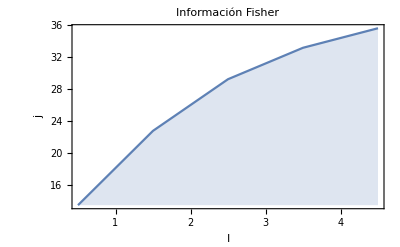

```mathematica
DiscretePlot[NIntegrate[ComplexExpand[(Abs[D[DensidadNormal[r,1,5,j+1/2,j-1/2],r]])^2/DensidadNormal[r,1,5,j+1/2,j-1/2]], {r, 0, 10}],{j,1/2,9/2,1},PlotRange->All, Joined->True,Frame->True,PlotLabel->"Información Fisher",FrameLabel->{"I","j"}]
```

```mathematica
DiscretePlot[NIntegrate[(Abs[D[DensidadNormalc[r,1,5,j+1/2,j-1/2],r]])^2/DensidadNormalc[r,1,5,j+1/2,j-1/2], {r, 0, 10}],{j,1/2,9/2,1},PlotRange->All, Joined->True]
```

```mathematica
{NIntegrate[ComplexExpand[(Abs[D[DensidadTotal[1,0,1/2,1/2,1,5,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotal[1,0,1/2,1/2,1,5,r,θ,ϕ]], {r, 0, 100},{θ,0,Pi},{ϕ,0,2*Pi}],NIntegrate[ComplexExpand[(Abs[D[DensidadTotal[2,1,3/2,1/2,1,5,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotal[2,1,3/2,1/2,1,5,r,θ,ϕ]], {r, 0, 100},{θ,0,Pi},{ϕ,0,2*Pi}],NIntegrate[ComplexExpand[(Abs[D[DensidadTotal[3,2,5/2,1/2,1,5,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotal[3,2,5/2,1/2,1,5,r,θ,ϕ]], {r, 0, 100},{θ,0,Pi},{ϕ,0,2*Pi}]}
```

```mathematica
NIntegrate[ComplexExpand[(Abs[D[DensidadTotal[3,2,5/2,1/2,1,5,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotal[3,2,5/2,1/2,1,5,r,θ,ϕ]], {r, 0, 100},{θ,0,Pi},{ϕ,0,2*Pi}]
```

```mathematica
Manipulate[(1.0/NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,5,r,θ,ϕ],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}])*NIntegrate[ComplexExpand[(Abs[D[DensidadTotal[j+1/2,j-1/2,j,eme,w,5,r,θ,ϕ],r]])^2/DensidadTotal[j+1/2,j-1/2,j,eme,w,5,r,θ,ϕ]],{r,0,10},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{j,1/2,9/2,1},{eme,1/2,7/2,1}]
```

```mathematica
TablaFisher = Table[{j,NIntegrate[ComplexExpand[(Abs[D[DensidadNormal[r,1,5,j+1/2,j-1/2],r]])^2/DensidadNormal[r,1,5,j+1/2,j-1/2]], {r, 0, 100}]},{j,0.5,4.5,1}]
```

```mathematica
TablaFisher //Flatten[#,0]&//Grid
```

```mathematica
TablaFisherc= Table[{j,NIntegrate[ComplexExpand[(Abs[D[DensidadNormalc[r,1,5,j+1/2,j-1/2],r]])^2/DensidadNormalc[r,1,5,j+1/2,j-1/2]], {r, 0, 100}]},{j,0.5,4.5,1}]
```

### Información de Fisher para j=1/2 (+), 3/2 y 5/2(-)fija y n (1,10):

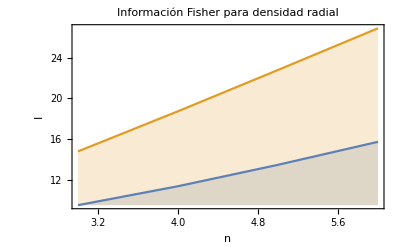

```mathematica
DiscretePlot[{NIntegrate[ComplexExpand[(Abs[D[DensidadNormal[r,1,n,1,0],r]])^2/DensidadNormal[r,1,n,1,0]], {r, 0, 10}],NIntegrate[ComplexExpand[(Abs[D[DensidadNormal[r,1,n,2,1],r]])^2/DensidadNormal[r,1,n,2,1]], {r, 0, 10}]},{n,3,6,1},PlotRange->All, Joined->True,Frame->True,PlotLabel->"Información Fisher para densidad radial",FrameLabel->{"n","I"}]
```

```mathematica
DiscretePlot[{NIntegrate[ComplexExpand[(Abs[D[DensidadNormalc[r,1,n,1,0],r]])^2/DensidadNormalc[r,1,n,1,0]], {r, 0, 10}],NIntegrate[ComplexExpand[(Abs[D[DensidadNormalc[r,1,n,2,1],r]])^2/DensidadNormalc[r,1,n,2,1]], {r, 0, 10}],NIntegrate[ComplexExpand[(Abs[D[DensidadNormalc[r,1,n,3,2],r]])^2/DensidadNormalc[r,1,n,3,2]], {r, 0, 10}]},{n,1,3,1},PlotRange->All, Joined->True]
```

```mathematica
DiscretePlot[{NIntegrate[ComplexExpand[Abs[D[DensidadTotalc[1,0,1/2,1/2,1,n,r,θ,ϕ],r,θ,ϕ]]^2/DensidadTotalc[1,0,1/2,1/2,1,n,r,θ,ϕ]], {r, 0, 10},{θ,0,Pi}{ϕ,0,2*Pi}],NIntegrate[ComplexExpand[Abs[D[DensidadTotalc[2,1,3/2,1/2,1,n,r,θ,ϕ],r,θ,ϕ]]^2/DensidadTotalc[2,1,3/2,1/2,1,n,r,θ,ϕ]], {r, 0, 10},{θ,0,Pi}{ϕ,0,2*Pi}],NIntegrate[ComplexExpand[Abs[D[DensidadTotalc[3,2,5/2,1/2,1,n,r,θ,ϕ],r,θ,ϕ]]^2/DensidadTotalc[3,2,5/2,1/2,1,n,r,θ,ϕ]], {r, 0, 10},{θ,0,Pi}{ϕ,0,2*Pi}]},{n,1,5,1},PlotRange->All, Joined->True]
```

```mathematica
TablaFisher2 = Table[{n,(1.0/NIntegrate[DensidadRadial[r,1,n,1,0],{r,0,10}])*NIntegrate[ComplexExpand[(Abs[D[DensidadRadial[r,1,n,1,0],r]])^2/DensidadRadial[r,1,n,1,0]], {r, 0, 10}],(1.0/NIntegrate[DensidadRadial[r,1,n,2,1],{r,0,10}])*NIntegrate[ComplexExpand[(Abs[D[DensidadRadial[r,1,n,2,1],r]])^2/DensidadRadial[r,1,n,2,1]], {r, 0, 10}],(1.0/NIntegrate[DensidadRadial[r,1,n,3,2],{r,0,10}])*NIntegrate[ComplexExpand[(Abs[D[DensidadRadial[r,1,n,3,2],r]])^2/DensidadRadial[r,1,n,3,2]], {r, 0, 10}]},{n,3,10,1}]
```

```mathematica
TablaFisher2 //Flatten[#,0]&//Grid
```

```mathematica
Fish[j_,eme_,n_]:=NIntegrate[ComplexExpand[(Abs[D[DensidadTotalc[j+1/2,j-1/2,j,eme,1,n,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotalc[j+1/2,j-1/2,j,eme,1,n,r,θ,ϕ]],{r, 1, 10},{θ,0,Pi},{ϕ,0,2*Pi}]
```

```mathematica
array10=Table[{j,Fish[j,3/2,5]},{j,1.5,4.5,1}]
```

```mathematica
TablaFisherTotal=Table[{j,eme,Fish[j,eme,5]},{j,1.5,4.5,1},{eme,{1/2,3/2}}]
TablaFisherTotalc=Table[{j,eme,NIntegrate[ComplexExpand[(Abs[D[DensidadTotalc[j+1/2,j-1/2,j,eme,1,5,r,θ,ϕ],r,θ,ϕ]])^2/DensidadTotalc[j+1/2,j-1/2,j,eme,1,5,r,θ,ϕ]],{r, 1, 10},{θ,0,Pi},{ϕ,0,2*Pi}]},{j,1.5,4.5,1},{eme,{1/2,3/2}}]
```

```mathematica
Desequilibrio:
```

```mathematica
Manipulate[(1.0/(NIntegrate[DensidadRadial[r,w,n,j+1/2,j-1/2],{r,0,100}])^2)*NIntegrate[DensidadRadial[r,w,n,j+1/2,j-1/2]^2, {r, 1, 100}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1}]
```

```mathematica
Manipulate[(1.0/(NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],{r,0,100},{θ,0,Pi},{ϕ,0,2*Pi}])^2)*NIntegrate[DensidadTotal[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ], {r, 1, 100},{θ,0,Pi},{ϕ,0,2*Pi}],{w,1,5,0.1},{n,1,10,1},{j,1/2,n-1/2,1},{eme,{1/2,3/2,5/2,7/2,9/2}}]
```

### Desequilibrio para n=5 fija y j variando:

```mathematica
DiscretePlot[NIntegrate[DensidadRadial[r,1,4,j+1/2,j-1/2]^2, {r, 0, 100}],{j,1/2,7/2,1},PlotRange->All, Joined->True,PlotLabel->"Desequilibrio en función de j",Frame->True]
DiscretePlot[NIntegrate[DensidadNormalc[r,1,6,j+1/2,j-1/2]^2, {r, 0, 100}],{j,1/2,11/2,1},PlotRange->All, Joined->True,PlotLabel->"Desequilibrio en función de j",Frame->True]
```

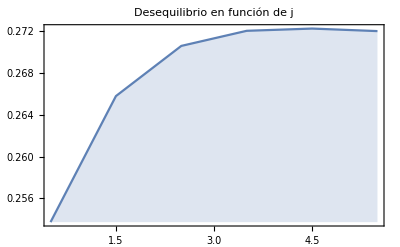

```mathematica
DiscretePlot[NIntegrate[DensidadNormalc[r,1,6,j+1/2,j-1/2]^2, {r, 0, 100}],{j,1/2,11/2,1},PlotRange->All, Joined->True,PlotLabel->"Desequilibrio en función de j",Frame->True]
```

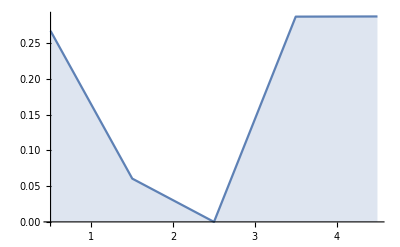

```mathematica
DiscretePlot[NIntegrate[(DensidadNormalc[r,1,5,j+1/2,j-1/2])^2, {r, 0, 100}],{j,1/2,9/2,1},PlotRange->All, Joined->True]
```

```mathematica
DiscretePlot[NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,1/2,1,4,r,θ,ϕ]^2, {r, 0, 100},{θ,0,Pi},{ϕ,0,2*Pi}],{j,1/2,7/2,1},PlotRange->All, Joined->True]
```

{{0.5,0.267475},{1.5,0.},{2.5,0.},{3.5,0.287426},{4.5,0.287681}}

### Desequilibrio para j=1/2 (+), 3/2 y 5/2(-)fija y n (1,10):

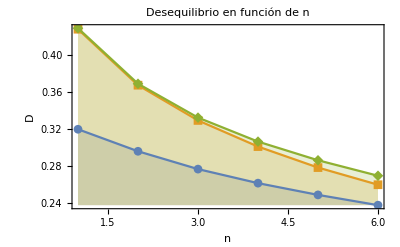

```mathematica
DiscretePlot[{(1.0/((NIntegrate[DensidadNormal[r,1,n,1,0],{r,0,100}])^2))*NIntegrate[(DensidadNormal[r,1,n,1,0])^2, {r, 1, 100}],(1.0/((NIntegrate[DensidadNormal[r,1,n,4,3],{r,0,100}])^2))*NIntegrate[(DensidadNormal[r,1,n,4,3])^2, {r, 1, 100}],(1.0/((NIntegrate[DensidadNormal[r,1,n,5,4],{r,0,100}])^2))*NIntegrate[(DensidadNormal[r,1,n,5,4])^2, {r, 1, 100}]},{n,1,6,1},PlotRange->All, Joined->True,Frame->True
,FrameLabel->{"n","D"}
,PlotMarkers->Automatic,PlotLabel->"Desequilibrio en función de n"]
```

Es raro...para n más grandes, me da error. Me da lo mismo densidad normal que normal c

```mathematica
nvaloress={2,3,4,5,6};
jvaloress={1/2,3/2};
Tablaa=Table[{n,(1.0/((NIntegrate[DensidadRadial[r,1,n,j+1/2,j-1/2],{r,0,100}])^2))*NIntegrate[(DensidadRadial[r,1,n,j+1/2,j-1/2])^2, {r, 0, 100}]},{j,jvaloress},{n,nvaloress}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{{2,0.343161},{3,0.308113},{4,0.28481},{5,0.267475},{6,0.253731}},{{2,0.356863},{3,0.322635},{4,0.298653},{5,0.},{6,0.265801}}}

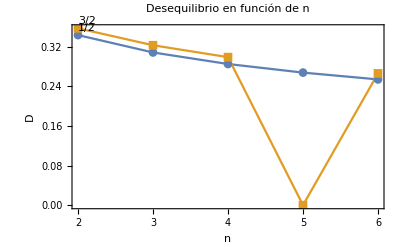

```mathematica
ListPlot[Tablaa
,Joined->True
,Frame->True
,FrameLabel->{"n","D"},PlotLabels->Placed[{"1/2","3/2"},Above]
,PlotMarkers->Automatic,PlotLabel->"Desequilibrio en función de n"]
```

```mathematica
TablaDesequilibrio2 = Table[{n,(1.0/(NIntegrate[DensidadRadial[r,1,n,1,0],{r,0,100}]^2))*NIntegrate[DensidadRadial[r,1,n,1,0]^2, {r, 1, 100}],(1.0/(NIntegrate[DensidadRadial[r,1,n,2,1],{r,0,100}]^2))*NIntegrate[DensidadRadial[r,1,n,2,1]^2, {r, 1, 100}],(1.0/(NIntegrate[DensidadRadial[r,1,n,3,2],{r,0,100}]^2))*NIntegrate[DensidadRadial[r,1,n,3,2]^2, {r, 1, 100}]},{n,1,6,1}]
```

{{1,0.319737,0.381826,0.421459},{2,0.295787,0.318105,0.356228},{3,0.27639,0.285305,0.313509},{4,0.261112,0.266975,0.283285},{5,0.248347,0.,0.},{6,0.237156,0.244921,0.247794}}

```mathematica
TablaDesequilibrio2//Flatten[#,0]&//Grid
```

```mathematica
des[j_,eme_,n_]:=(1.0/(NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,1,n,r,θ,ϕ],{r,0,100},{θ,0,Pi},{ϕ,0,2*Pi}]^2))*NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,1,n,r,θ,ϕ]^2, {r, 1, 100},{θ,0,Pi},{ϕ,0,2*Pi}]
```

```mathematica
TablaDesequilibrioTotal = Table[{n,des[1/2,1/2,n][[1,1]]},{n,1,6,1}]
```

{{1,0.0176856},{2,0.0163609},{3,0.015288},{4,0.0144429},{5,0.0137368},{6,0.0131179}}

No me permite más valores de n

{{1,{{0.0176856}}},{2,{{0.0163609}}},{3,{{0.015288}}},{4,{{0.0144429}}},{5,{{0.0137368}}},{6,{{0.0131179}}}}

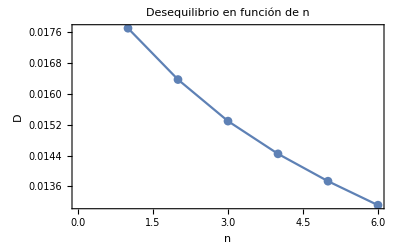

```mathematica
ListPlot[TablaDesequilibrioTotal
,Joined->True
,Frame->True
,FrameLabel->{"n","D"}
,PlotMarkers->Automatic,PlotLabel->"Desequilibrio en función de n"]
```

```mathematica
emevalores1={1/2,3/2,5/2}
```

{1/2,3/2,5/2}

```mathematica
TablaDesequilibrioTotal1 = Table[{j,des[j,eme,6][[1,1]]},{eme,emevalores1},{j,5/2,11/2,1}]
```

{{{5/2,0.0181077},{7/2,0.0213348},{9/2,0.0244887},{11/2,0.026598}},{{5/2,0.0158998},{7/2,0.0173236},{9/2,0.0188623},{11/2,0.0199025}},{{5/2,0.0195342},{7/2,0.0191311},{9/2,0.0197733},{11/2,0.0202512}}}

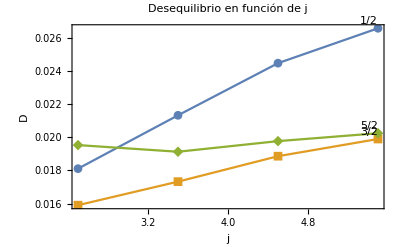

```mathematica
ListPlot[TablaDesequilibrioTotal1
,Joined->True
,Frame->True
,FrameLabel->{"j","D"}
,PlotMarkers->Automatic,PlotLabel->"Desequilibrio en función de j",
PlotLabels->Placed[{"1/2","3/2","5/2"},Above]]
```

```mathematica
,PlotLabels->Placed[{"D"},Above]
```

```mathematica
jvaloreseme={7/2,9/2,11/2};
TablaDesequilibrioTotal2 = Table[{eme,des[7/2,eme,6][[1,1]]},{eme,1/2,9/2,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1/2,0.0213348},{3/2,0.0173236},{5/2,0.0191311},{7/2,0.0237987},{9/2,0.034515}}

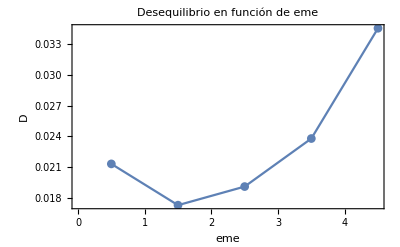

```mathematica
ListPlot[TablaDesequilibrioTotal2
,Joined->True
,Frame->True
,FrameLabel->{"eme","D"}
,PlotMarkers->Automatic,PlotLabel->"Desequilibrio en función de eme"]
```

```mathematica
dese[j_,eme_,n_,w_]:=(1.0/(NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ],{r,0,100},{θ,0,Pi},{ϕ,0,2*Pi}]^2))*NIntegrate[DensidadTotalc[j+1/2,j-1/2,j,eme,w,n,r,θ,ϕ]^2, {r, 1, 100},{θ,0,Pi},{ϕ,0,2*Pi}]
```

```mathematica
wvalores={1,3,5,7};
```

```mathematica
TablaDesequilibrioTotal = Table[{w,dese[1/2,1/2,4,w][[1,1]]},{w,wvalores}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1,0.0144429},{3,0.0232409},{5,0.0274463},{7,0.0317974}}

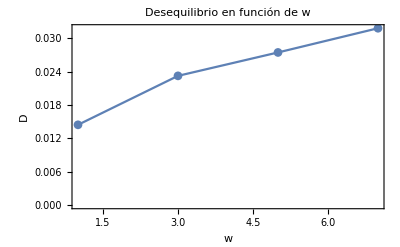

```mathematica
ListPlot[TablaDesequilibrioTotal
,Joined->True
,Frame->True
,FrameLabel->{"w","D"},
PlotRange->All
,PlotMarkers->Automatic,PlotLabel->"Desequilibrio en función de w"]
```

```mathematica
Medidas de complejidad:
```

```mathematica
jota[j_,eme_,w_,n_]:=(1/(2*Pi*E))*E^(2/3*int[j,eme,w,n])
CFS[j_,eme_,w_,n_]:=Fish[j,eme,n]*jota[j,eme,w,n]
CLM[j_,eme_,w_,n_]:=des[j,eme,n]*E^(int[j,eme,w,n])
CLM[1/2,1/2,1,3]
CFS[1/2,1/2,1,3]
jota[1/2,1/2,1,3]
```

{{1.09232}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.+0. ⅈ}}

{{1.00815}}

```mathematica
emevaloresc={1/2,3/2,5/2,7/2};
jvaloresc={7/2,9/2,11/2};
nvaloresc={1,2,3,4,5,6};
```

```mathematica
TablaCLM=Table[{eme,CLM[j,eme,1,6][[1,1]]},{j,jvaloresc},{eme,emevaloresc}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.026598 and 6.75494×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0199025 and 4.21437×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0202512 and 1.36455×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{{1/2,1.40262},{3/2,1.25409},{5/2,1.22686},{7/2,1.22148}},{{1/2,1.51959},{3/2,1.33707},{5/2,1.29793},{7/2,1.27491}},{{1/2,1.57352},{3/2,1.38159},{5/2,1.33877},{7/2,1.30826}}}

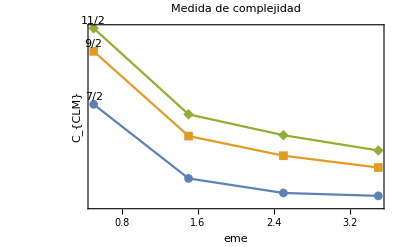

```mathematica
ListLogPlot[TablaCLM
,Joined->True,PlotRange->All
,Frame->True
,FrameLabel->{"eme","C_{CLM}"}
,PlotMarkers->Automatic,PlotLabel->"Medida de complejidad",PlotLabels->Placed[{"7/2","9/2","11/2"},Above]]
```

```mathematica
ListLogPlot[TablaCLM
,Joined->True,PlotRange->All
,Frame->True
,FrameLabel->{"eme","C_{CLM}"}
,PlotMarkers->Automatic,PlotLabel->"Medida de complejidad",PlotLabels->Placed[{"7/2","9/2","11/2"},Above]]
```

-Graphics-

```mathematica
TablaCLM=Table[{j,CLM[j,eme,1,6][[1,1]]},{eme,emevaloresc},{j,jvaloresc}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.026598 and 6.75494×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0199025 and 4.21437×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0202512 and 1.36455×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{{7/2,1.40262},{9/2,1.51959},{11/2,1.57352}},{{7/2,1.25409},{9/2,1.33707},{11/2,1.38159}},{{7/2,1.22686},{9/2,1.29793},{11/2,1.33877}},{{7/2,1.22148},{9/2,1.27491},{11/2,1.30826}}}

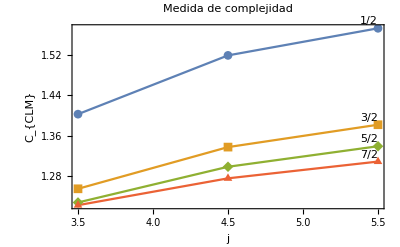

```mathematica
ListPlot[TablaCLM
,Joined->True,PlotRange->All
,Frame->True
,FrameLabel->{"j","C_{CLM}"}
,PlotMarkers->Automatic,PlotLabel->"Medida de complejidad",PlotLabels->Placed[{"1/2","3/2","5/2","7/2"},Above]]
```

```mathematica
FishRadial[j_,w_,n_]:=NIntegrate[ComplexExpand[(Abs[D[DensidadNormal[r,w,n,j+1/2,j-1/2],r]])^2/DensidadNormal[r,w,n,j+1/2,j-1/2]],{r, 1, 10}]
intRadial[j_,w_,n_]:=-1.0*NIntegrate[DensidadNormal[r,w,n,j+1/2,j-1/2]*Log[DensidadNormal[r,w,n,j+1/2,j-1/2]],{r,0,10}]
jotaRadial[j_,w_,n_]:=(1/(2*Pi*E))*E^(2/3*intRadial[j,w,n])
```

```mathematica
CFSRadial[j_,w_,n_]:=FishRadial[j,w,n]*jotaRadial[j,w,n]
```

```mathematica
TablaCFSR=Table[{w,CFSRadial[1/2,w,6]},{w,{1,3,5}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.32017}. NIntegrate obtained 12.4348+0. ⅈ and 0.000382284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.00181}. NIntegrate obtained 33.6633+0. ⅈ and 0.00127031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.20610887394228}. NIntegrate obtained 49.7499+0. ⅈ and 0.00342957 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1,2.05277},{3,3.85318},{5,4.80292}}

```mathematica
Dimensions[CFSRadial[j,w,n]]
```

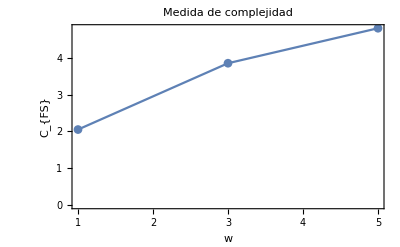

```mathematica
ListPlot[TablaCFSR
,Joined->True,PlotRange->All
,Frame->True
,FrameLabel->{"w","C_{FS}"}
,PlotMarkers->Automatic,PlotLabel->"Medida de complejidad"]
```

### Otros momentos de frecuencia